```mathematica
AR[Tr_,t_]:=(1+t/Tr)^-2
```

```mathematica
I1[Tr_,tau1_,t_]:=AR[Tr,t]*(Exp[-t/tau1]/tau1)
```

```mathematica
IR1[t_]:=I1[15.,2.2,t]
```

```mathematica
CIR1 = Integrate[IR1[t],{t,0., Infinity}]
```

0.790579

```mathematica
IR2[t_]:=I1[15.,27.,t]
```

```mathematica
CIR2 = Integrate[IR2[t],{t,0., Infinity}]
```

0.287889

```mathematica
Integrate[IR1[t]/CIR1,{t,0., Infinity}]
```

1.

```mathematica
IN1[t_]:=IR1[t]/CIR1
```

```mathematica
Integrate[IN1[t],{t,0., Infinity}]
```

1.

```mathematica
IN2[t_]:=IR2[t]/CIR2
```

```mathematica
Integrate[IN2[t],{t,0., Infinity}]
```

1.

```mathematica
AA[x_]:=x/(1+x)
```

```mathematica
AA[0.17]
```

0.145299

```mathematica
AA[0.8]
```

0.444444

```mathematica
IN[t_]:=0.45*IN1[t]+0.55*IN2[t]
```

```mathematica
Integrate[IN[t],{t,0., Infinity}]
```

1.

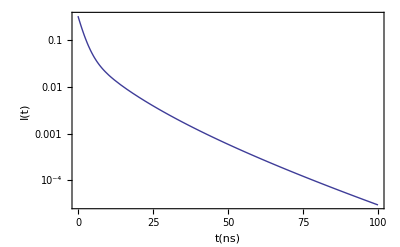

```mathematica
LogPlot[IN[t],{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","I(t)"}]
```

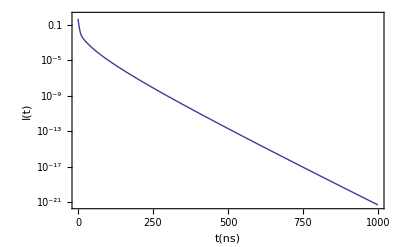

```mathematica
LogPlot[IN[t],{t,0.,1000.},Frame->True,FrameLabel->{"t(ns)","I(t)"}]
```

```mathematica
Integrate[IN[t],{t,0., Infinity}]
```

1.

```mathematica
IS[t_,tau_]:=Exp[-t/tau]/tau
```

```mathematica
IS1[t_]:=IS[t,2.2]
IS2[t_]:=IS[t,27.]
```

```mathematica
Integrate[IS2[t],{t,0., Infinity}]
```

1.

```mathematica
ITS[t_]:=0.15*IS1[t]+0.85*IS2[t]
```

```mathematica
Integrate[ITS[t],{t,0., Infinity}]
```

1.

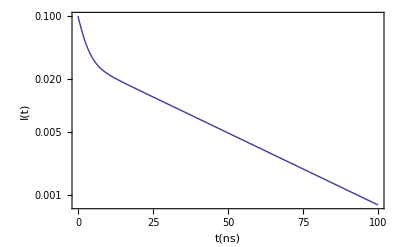

```mathematica
LogPlot[ITS[t],{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","I(t)"}]
```

```mathematica
IX[t_]:=0.71*IN[t]+0.29*ITS[t]
```

```mathematica
Integrate[IX[t],{t,0., Infinity}]
```

1.

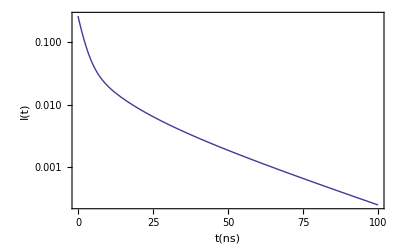

```mathematica
LogPlot[IX[t],{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","I(t)"}]
```

```mathematica
AX[t_]:=(3*10^4)*IX[t]
```

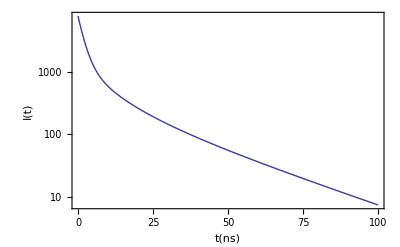

```mathematica
LogPlot[AX[t],{t,0.,100.},Frame->True,FrameLabel->{"t(ns)","I(t)"}]
```

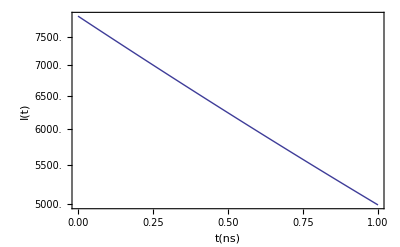

```mathematica
LogPlot[AX[t],{t,0.,1.},Frame->True,FrameLabel->{"t(ns)","I(t)"}]
```

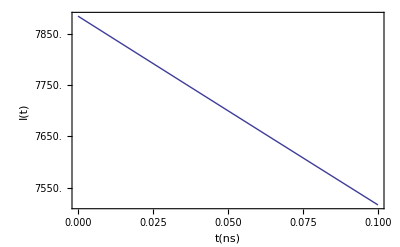

```mathematica
LogPlot[AX[t],{t,0.,0.1},Frame->True,FrameLabel->{"t(ns)","I(t)"}]
```

```mathematica
Integrate[AX[t],{t,0., Infinity}]
```

30000.

```mathematica
fp=Table[{x,AX[x]},{x,0.,10.,0.05}]
```

{{0.,7885.13},{0.05,7698.96},{0.1,7517.96},{0.15,7341.99},{0.2,7170.89},{0.25,7004.52},{0.3,6842.74},{0.35,6685.42},{0.4,6532.42},{0.45,6383.63},{0.5,6238.91},{0.55,6098.14},{0.6,5961.22},{0.65,5828.02},{0.7,5698.44},{0.75,5572.38},{0.8,5449.73},{0.85,5330.39},{0.9,5214.27},{0.95,5101.28},{1.,4991.32},{1.05,4884.3},{1.1,4780.14},{1.15,4678.76},{1.2,4580.09},{1.25,4484.03},{1.3,4390.52},{1.35,4299.48},{1.4,4210.84},{1.45,4124.54},{1.5,4040.5},{1.55,3958.67},{1.6,3878.98},{1.65,3801.36},{1.7,3725.77},{1.75,3652.13},{1.8,3580.41},{1.85,3510.54},{1.9,3442.47},{1.95,3376.15},{2.,3311.53},{2.05,3248.56},{2.1,3187.2},{2.15,3127.41},{2.2,3069.13},{2.25,3012.33},{2.3,2956.96},{2.35,2902.98},{2.4,2850.36},{2.45,2799.06},{2.5,2749.05},{2.55,2700.27},{2.6,2652.71},{2.65,2606.33},{2.7,2561.09},{2.75,2516.97},{2.8,2473.93},{2.85,2431.94},{2.9,2390.98},{2.95,2351.02},{3.,2312.02},{3.05,2273.97},{3.1,2236.84},{3.15,2200.6},{3.2,2165.22},{3.25,2130.69},{3.3,2096.99},{3.35,2064.08},{3.4,2031.95},{3.45,2000.58},{3.5,1969.94},{3.55,1940.02},{3.6,1910.8},{3.65,1882.26},{3.7,1854.37},{3.75,1827.13},{3.8,1800.52},{3.85,1774.52},{3.9,1749.11},{3.95,1724.28},{4.,1700.},{4.05,1676.28},{4.1,1653.09},{4.15,1630.42},{4.2,1608.25},{4.25,1586.58},{4.3,1565.38},{4.35,1544.65},{4.4,1524.38},{4.45,1504.55},{4.5,1485.15},{4.55,1466.17},{4.6,1447.6},{4.65,1429.42},{4.7,1411.64},{4.75,1394.23},{4.8,1377.19},{4.85,1360.51},{4.9,1344.18},{4.95,1328.2},{5.,1312.54},{5.05,1297.21},{5.1,1282.19},{5.15,1267.48},{5.2,1253.07},{5.25,1238.95},{5.3,1225.12},{5.35,1211.57},{5.4,1198.28},{5.45,1185.26},{5.5,1172.5},{5.55,1159.99},{5.6,1147.72},{5.65,1135.7},{5.7,1123.9},{5.75,1112.33},{5.8,1100.99},{5.85,1089.86},{5.9,1078.94},{5.95,1068.22},{6.,1057.71},{6.05,1047.39},{6.1,1037.26},{6.15,1027.32},{6.2,1017.57},{6.25,1007.99},{6.3,998.578},{6.35,989.339},{6.4,980.266},{6.45,971.354},{6.5,962.599},{6.55,953.998},{6.6,945.546},{6.65,937.242},{6.7,929.08},{6.75,921.058},{6.8,913.172},{6.85,905.42},{6.9,897.797},{6.95,890.302},{7.,882.931},{7.05,875.681},{7.1,868.55},{7.15,861.535},{7.2,854.633},{7.25,847.842},{7.3,841.159},{7.35,834.581},{7.4,828.107},{7.45,821.734},{7.5,815.46},{7.55,809.282},{7.6,803.199},{7.65,797.208},{7.7,791.308},{7.75,785.496},{7.8,779.77},{7.85,774.128},{7.9,768.57},{7.95,763.092},{8.,757.693},{8.05,752.372},{8.1,747.127},{8.15,741.956},{8.2,736.857},{8.25,731.83},{8.3,726.872},{8.35,721.982},{8.4,717.159},{8.45,712.402},{8.5,707.708},{8.55,703.077},{8.6,698.507},{8.65,693.997},{8.7,689.547},{8.75,685.153},{8.8,680.817},{8.85,676.536},{8.9,672.309},{8.95,668.135},{9.,664.013},{9.05,659.942},{9.1,655.922},{9.15,651.95},{9.2,648.027},{9.25,644.151},{9.3,640.321},{9.35,636.537},{9.4,632.797},{9.45,629.101},{9.5,625.448},{9.55,621.837},{9.6,618.267},{9.65,614.738},{9.7,611.248},{9.75,607.797},{9.8,604.385},{9.85,601.01},{9.9,597.672},{9.95,594.37},{10.,591.104}}

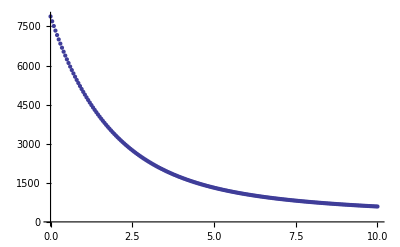

```mathematica
gp=ListPlot[fp]
```

```mathematica
FindFit[fp,a*Exp[x/2.2]/2.2+ b*Exp[x/27]/27,{a,b},x]
```

{a→-7.60691×10^-18,b→87.9135}

```mathematica
model =a*Exp[-k*t]
```

a ⅇ^(-k t)

```mathematica
fit = FindFit[fp,model,{a,k},t]
```

{a→7205.78,k→0.346863}

```mathematica
modelf=Function[{t},Evaluate[model/.fit]]
```

Function[{t},7205.78 ⅇ^(-0.346863 t)]

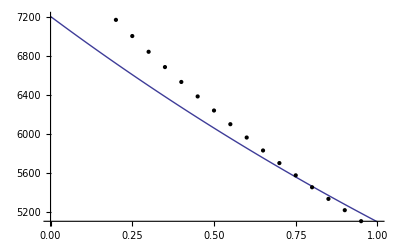

```mathematica
Plot[modelf[t],{t,0,1},Epilog->Map[Point,fp]]
```

```mathematica
model2 =a*Exp[-k1*t]+b*Exp[-k2*t]
```

a ⅇ^(-k1 t)+b ⅇ^(-k2 t)

```mathematica
fit2 = FindFit[fp,model2,{a,b,k1,k2},t]
```

{a→6293.67,b→1581.09,k1→0.566997,k2→0.103275}

```mathematica
modelf2=Function[{t},Evaluate[model2/.fit2]]
```

Function[{t},6293.67 ⅇ^(-0.566997 t)+1581.09 ⅇ^(-0.103275 t)]

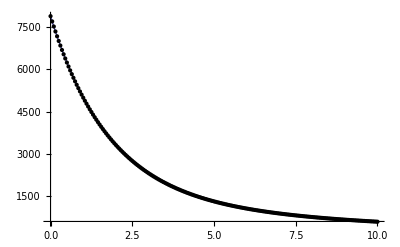

```mathematica
Plot[modelf2[t],{t,0,10},Epilog->Map[Point,fp]]
```

```mathematica
fp=Table[{x,AX[x]},{x,0.,100.,0.1}]
```

{{0.,7885.13},{0.1,7517.96},{0.2,7170.89},{0.3,6842.74},{0.4,6532.42},{0.5,6238.91},{0.6,5961.22},{0.7,5698.44},{0.8,5449.73},{0.9,5214.27},{1.,4991.32},{1.1,4780.14},{1.2,4580.09},{1.3,4390.52},{1.4,4210.84},{1.5,4040.5},{1.6,3878.98},{1.7,3725.77},{1.8,3580.41},{1.9,3442.47},{2.,3311.53},{2.1,3187.2},{2.2,3069.13},{2.3,2956.96},{2.4,2850.36},{2.5,2749.05},{2.6,2652.71},{2.7,2561.09},{2.8,2473.93},{2.9,2390.98},{3.,2312.02},{3.1,2236.84},{3.2,2165.22},{3.3,2096.99},{3.4,2031.95},{3.5,1969.94},{3.6,1910.8},{3.7,1854.37},{3.8,1800.52},{3.9,1749.11},{4.,1700.},{4.1,1653.09},{4.2,1608.25},{4.3,1565.38},{4.4,1524.38},{4.5,1485.15},{4.6,1447.6},{4.7,1411.64},{4.8,1377.19},{4.9,1344.18},{5.,1312.54},{5.1,1282.19},{5.2,1253.07},{5.3,1225.12},{5.4,1198.28},{5.5,1172.5},{5.6,1147.72},{5.7,1123.9},{5.8,1100.99},{5.9,1078.94},{6.,1057.71},{6.1,1037.26},{6.2,1017.57},{6.3,998.578},{6.4,980.266},{6.5,962.599},{6.6,945.546},{6.7,929.08},{6.8,913.172},{6.9,897.797},{7.,882.931},{7.1,868.55},{7.2,854.633},{7.3,841.159},{7.4,828.107},{7.5,815.46},{7.6,803.199},{7.7,791.308},{7.8,779.77},{7.9,768.57},{8.,757.693},{8.1,747.127},{8.2,736.857},{8.3,726.872},{8.4,717.159},{8.5,707.708},{8.6,698.507},{8.7,689.547},{8.8,680.817},{8.9,672.309},{9.,664.013},{9.1,655.922},{9.2,648.027},{9.3,640.321},{9.4,632.797},{9.5,625.448},{9.6,618.267},{9.7,611.248},{9.8,604.385},{9.9,597.672},{10.,591.104},{10.1,584.676},{10.2,578.383},{10.3,572.22},{10.4,566.183},{10.5,560.267},{10.6,554.468},{10.7,548.783},{10.8,543.207},{10.9,537.737},{11.,532.37},{11.1,527.102},{11.2,521.93},{11.3,516.851},{11.4,511.862},{11.5,506.961},{11.6,502.145},{11.7,497.411},{11.8,492.757},{11.9,488.18},{12.,483.679},{12.1,479.251},{12.2,474.894},{12.3,470.607},{12.4,466.386},{12.5,462.231},{12.6,458.14},{12.7,454.111},{12.8,450.142},{12.9,446.232},{13.,442.379},{13.1,438.582},{13.2,434.84},{13.3,431.151},{13.4,427.514},{13.5,423.927},{13.6,420.39},{13.7,416.901},{13.8,413.459},{13.9,410.064},{14.,406.713},{14.1,403.407},{14.2,400.144},{14.3,396.922},{14.4,393.742},{14.5,390.603},{14.6,387.503},{14.7,384.441},{14.8,381.418},{14.9,378.432},{15.,375.482},{15.1,372.568},{15.2,369.688},{15.3,366.843},{15.4,364.032},{15.5,361.254},{15.6,358.508},{15.7,355.794},{15.8,353.111},{15.9,350.459},{16.,347.836},{16.1,345.244},{16.2,342.68},{16.3,340.145},{16.4,337.638},{16.5,335.158},{16.6,332.706},{16.7,330.28},{16.8,327.88},{16.9,325.506},{17.,323.158},{17.1,320.834},{17.2,318.535},{17.3,316.259},{17.4,314.008},{17.5,311.78},{17.6,309.575},{17.7,307.393},{17.8,305.232},{17.9,303.094},{18.,300.978},{18.1,298.883},{18.2,296.808},{18.3,294.755},{18.4,292.722},{18.5,290.708},{18.6,288.715},{18.7,286.741},{18.8,284.787},{18.9,282.851},{19.,280.934},{19.1,279.036},{19.2,277.155},{19.3,275.293},{19.4,273.448},{19.5,271.621},{19.6,269.811},{19.7,268.018},{19.8,266.241},{19.9,264.481},{20.,262.738},{20.1,261.01},{20.2,259.299},{20.3,257.603},{20.4,255.923},{20.5,254.257},{20.6,252.607},{20.7,250.972},{20.8,249.352},{20.9,247.746},{21.,246.154},{21.1,244.577},{21.2,243.013},{21.3,241.463},{21.4,239.927},{21.5,238.405},{21.6,236.895},{21.7,235.399},{21.8,233.916},{21.9,232.446},{22.,230.988},{22.1,229.543},{22.2,228.11},{22.3,226.69},{22.4,225.281},{22.5,223.885},{22.6,222.5},{22.7,221.127},{22.8,219.766},{22.9,218.416},{23.,217.077},{23.1,215.749},{23.2,214.433},{23.3,213.127},{23.4,211.832},{23.5,210.548},{23.6,209.274},{23.7,208.011},{23.8,206.758},{23.9,205.515},{24.,204.282},{24.1,203.059},{24.2,201.846},{24.3,200.643},{24.4,199.45},{24.5,198.265},{24.6,197.091},{24.7,195.926},{24.8,194.769},{24.9,193.622},{25.,192.485},{25.1,191.356},{25.2,190.235},{25.3,189.124},{25.4,188.021},{25.5,186.927},{25.6,185.841},{25.7,184.764},{25.8,183.695},{25.9,182.634},{26.,181.582},{26.1,180.537},{26.2,179.5},{26.3,178.472},{26.4,177.451},{26.5,176.437},{26.6,175.432},{26.7,174.434},{26.8,173.443},{26.9,172.46},{27.,171.484},{27.1,170.516},{27.2,169.554},{27.3,168.6},{27.4,167.653},{27.5,166.713},{27.6,165.78},{27.7,164.853},{27.8,163.933},{27.9,163.021},{28.,162.114},{28.1,161.215},{28.2,160.321},{28.3,159.435},{28.4,158.554},{28.5,157.68},{28.6,156.812},{28.7,155.951},{28.8,155.096},{28.9,154.246},{29.,153.403},{29.1,152.566},{29.2,151.734},{29.3,150.909},{29.4,150.089},{29.5,149.275},{29.6,148.467},{29.7,147.665},{29.8,146.868},{29.9,146.076},{30.,145.29},{30.1,144.51},{30.2,143.735},{30.3,142.965},{30.4,142.201},{30.5,141.441},{30.6,140.687},{30.7,139.939},{30.8,139.195},{30.9,138.456},{31.,137.723},{31.1,136.994},{31.2,136.27},{31.3,135.551},{31.4,134.837},{31.5,134.128},{31.6,133.424},{31.7,132.724},{31.8,132.029},{31.9,131.338},{32.,130.652},{32.1,129.971},{32.2,129.294},{32.3,128.622},{32.4,127.954},{32.5,127.29},{32.6,126.631},{32.7,125.976},{32.8,125.326},{32.9,124.679},{33.,124.037},{33.1,123.399},{33.2,122.765},{33.3,122.136},{33.4,121.51},{33.5,120.888},{33.6,120.271},{33.7,119.657},{33.8,119.047},{33.9,118.441},{34.,117.839},{34.1,117.241},{34.2,116.647},{34.3,116.056},{34.4,115.469},{34.5,114.886},{34.6,114.306},{34.7,113.731},{34.8,113.158},{34.9,112.59},{35.,112.025},{35.1,111.463},{35.2,110.905},{35.3,110.35},{35.4,109.799},{35.5,109.251},{35.6,108.707},{35.7,108.166},{35.8,107.628},{35.9,107.094},{36.,106.563},{36.1,106.035},{36.2,105.511},{36.3,104.989},{36.4,104.471},{36.5,103.956},{36.6,103.444},{36.7,102.935},{36.8,102.429},{36.9,101.927},{37.,101.427},{37.1,100.93},{37.2,100.437},{37.3,99.9458},{37.4,99.458},{37.5,98.9731},{37.6,98.4911},{37.7,98.012},{37.8,97.5357},{37.9,97.0622},{38.,96.5916},{38.1,96.1237},{38.2,95.6586},{38.3,95.1962},{38.4,94.7366},{38.5,94.2796},{38.6,93.8254},{38.7,93.3737},{38.8,92.9248},{38.9,92.4784},{39.,92.0347},{39.1,91.5935},{39.2,91.1549},{39.3,90.7188},{39.4,90.2852},{39.5,89.8542},{39.6,89.4256},{39.7,88.9995},{39.8,88.5759},{39.9,88.1546},{40.,87.7358},{40.1,87.3194},{40.2,86.9054},{40.3,86.4937},{40.4,86.0844},{40.5,85.6774},{40.6,85.2727},{40.7,84.8703},{40.8,84.4702},{40.9,84.0723},{41.,83.6767},{41.1,83.2833},{41.2,82.8921},{41.3,82.5031},{41.4,82.1163},{41.5,81.7317},{41.6,81.3492},{41.7,80.9688},{41.8,80.5906},{41.9,80.2145},{42.,79.8404},{42.1,79.4685},{42.2,79.0986},{42.3,78.7307},{42.4,78.3649},{42.5,78.001},{42.6,77.6392},{42.7,77.2794},{42.8,76.9216},{42.9,76.5657},{43.,76.2117},{43.1,75.8597},{43.2,75.5097},{43.3,75.1615},{43.4,74.8152},{43.5,74.4708},{43.6,74.1283},{43.7,73.7876},{43.8,73.4488},{43.9,73.1118},{44.,72.7766},{44.1,72.4433},{44.2,72.1117},{44.3,71.7819},{44.4,71.4539},{44.5,71.1276},{44.6,70.8031},{44.7,70.4803},{44.8,70.1593},{44.9,69.8399},{45.,69.5223},{45.1,69.2063},{45.2,68.8921},{45.3,68.5795},{45.4,68.2685},{45.5,67.9592},{45.6,67.6515},{45.7,67.3455},{45.8,67.0411},{45.9,66.7382},{46.,66.437},{46.1,66.1373},{46.2,65.8392},{46.3,65.5427},{46.4,65.2477},{46.5,64.9543},{46.6,64.6624},{46.7,64.372},{46.8,64.0832},{46.9,63.7958},{47.,63.5099},{47.1,63.2255},{47.2,62.9426},{47.3,62.6611},{47.4,62.3811},{47.5,62.1026},{47.6,61.8255},{47.7,61.5498},{47.8,61.2755},{47.9,61.0026},{48.,60.7312},{48.1,60.4611},{48.2,60.1924},{48.3,59.9251},{48.4,59.6591},{48.5,59.3945},{48.6,59.1312},{48.7,58.8693},{48.8,58.6087},{48.9,58.3495},{49.,58.0915},{49.1,57.8349},{49.2,57.5796},{49.3,57.3255},{49.4,57.0727},{49.5,56.8213},{49.6,56.571},{49.7,56.3221},{49.8,56.0743},{49.9,55.8279},{50.,55.5826},{50.1,55.3386},{50.2,55.0958},{50.3,54.8543},{50.4,54.6139},{50.5,54.3747},{50.6,54.1368},{50.7,53.9},{50.8,53.6643},{50.9,53.4299},{51.,53.1966},{51.1,52.9645},{51.2,52.7335},{51.3,52.5037},{51.4,52.275},{51.5,52.0474},{51.6,51.821},{51.7,51.5956},{51.8,51.3714},{51.9,51.1483},{52.,50.9263},{52.1,50.7053},{52.2,50.4855},{52.3,50.2667},{52.4,50.049},{52.5,49.8323},{52.6,49.6168},{52.7,49.4022},{52.8,49.1887},{52.9,48.9763},{53.,48.7649},{53.1,48.5545},{53.2,48.3451},{53.3,48.1368},{53.4,47.9294},{53.5,47.7231},{53.6,47.5177},{53.7,47.3134},{53.8,47.11},{53.9,46.9076},{54.,46.7062},{54.1,46.5058},{54.2,46.3063},{54.3,46.1078},{54.4,45.9102},{54.5,45.7136},{54.6,45.5179},{54.7,45.3231},{54.8,45.1293},{54.9,44.9365},{55.,44.7445},{55.1,44.5534},{55.2,44.3633},{55.3,44.1741},{55.4,43.9857},{55.5,43.7983},{55.6,43.6117},{55.7,43.4261},{55.8,43.2413},{55.9,43.0574},{56.,42.8743},{56.1,42.6922},{56.2,42.5108},{56.3,42.3304},{56.4,42.1508},{56.5,41.972},{56.6,41.7941},{56.7,41.617},{56.8,41.4407},{56.9,41.2653},{57.,41.0907},{57.1,40.9169},{57.2,40.744},{57.3,40.5718},{57.4,40.4004},{57.5,40.2299},{57.6,40.0601},{57.7,39.8912},{57.8,39.723},{57.9,39.5556},{58.,39.389},{58.1,39.2231},{58.2,39.058},{58.3,38.8937},{58.4,38.7302},{58.5,38.5674},{58.6,38.4054},{58.7,38.2441},{58.8,38.0835},{58.9,37.9238},{59.,37.7647},{59.1,37.6064},{59.2,37.4488},{59.3,37.2919},{59.4,37.1358},{59.5,36.9803},{59.6,36.8256},{59.7,36.6716},{59.8,36.5183},{59.9,36.3657},{60.,36.2138},{60.1,36.0626},{60.2,35.9121},{60.3,35.7623},{60.4,35.6132},{60.5,35.4647},{60.6,35.3169},{60.7,35.1698},{60.8,35.0234},{60.9,34.8776},{61.,34.7325},{61.1,34.5881},{61.2,34.4443},{61.3,34.3012},{61.4,34.1587},{61.5,34.0168},{61.6,33.8756},{61.7,33.7351},{61.8,33.5952},{61.9,33.4559},{62.,33.3172},{62.1,33.1792},{62.2,33.0418},{62.3,32.905},{62.4,32.7688},{62.5,32.6332},{62.6,32.4983},{62.7,32.3639},{62.8,32.2302},{62.9,32.0971},{63.,31.9645},{63.1,31.8326},{63.2,31.7012},{63.3,31.5704},{63.4,31.4402},{63.5,31.3106},{63.6,31.1816},{63.7,31.0532},{63.8,30.9253},{63.9,30.798},{64.,30.6713},{64.1,30.5451},{64.2,30.4195},{64.3,30.2944},{64.4,30.17},{64.5,30.046},{64.6,29.9226},{64.7,29.7998},{64.8,29.6775},{64.9,29.5557},{65.,29.4345},{65.1,29.3138},{65.2,29.1937},{65.3,29.0741},{65.4,28.955},{65.5,28.8365},{65.6,28.7184},{65.7,28.6009},{65.8,28.4839},{65.9,28.3674},{66.,28.2515},{66.1,28.136},{66.2,28.0211},{66.3,27.9066},{66.4,27.7927},{66.5,27.6793},{66.6,27.5663},{66.7,27.4539},{66.8,27.3419},{66.9,27.2305},{67.,27.1195},{67.1,27.009},{67.2,26.899},{67.3,26.7895},{67.4,26.6804},{67.5,26.5719},{67.6,26.4638},{67.7,26.3562},{67.8,26.249},{67.9,26.1423},{68.,26.0361},{68.1,25.9303},{68.2,25.8251},{68.3,25.7202},{68.4,25.6158},{68.5,25.5119},{68.6,25.4084},{68.7,25.3054},{68.8,25.2028},{68.9,25.1007},{69.,24.999},{69.1,24.8977},{69.2,24.7969},{69.3,24.6965},{69.4,24.5966},{69.5,24.4971},{69.6,24.398},{69.7,24.2993},{69.8,24.2011},{69.9,24.1033},{70.,24.0059},{70.1,23.9089},{70.2,23.8124},{70.3,23.7163},{70.4,23.6206},{70.5,23.5252},{70.6,23.4303},{70.7,23.3359},{70.8,23.2418},{70.9,23.1481},{71.,23.0548},{71.1,22.9619},{71.2,22.8695},{71.3,22.7774},{71.4,22.6857},{71.5,22.5944},{71.6,22.5035},{71.7,22.413},{71.8,22.3228},{71.9,22.2331},{72.,22.1437},{72.1,22.0548},{72.2,21.9662},{72.3,21.8779},{72.4,21.7901},{72.5,21.7026},{72.6,21.6155},{72.7,21.5288},{72.8,21.4424},{72.9,21.3564},{73.,21.2708},{73.1,21.1856},{73.2,21.1007},{73.3,21.0161},{73.4,20.9319},{73.5,20.8481},{73.6,20.7646},{73.7,20.6815},{73.8,20.5988},{73.9,20.5163},{74.,20.4343},{74.1,20.3526},{74.2,20.2712},{74.3,20.1902},{74.4,20.1095},{74.5,20.0291},{74.6,19.9491},{74.7,19.8695},{74.8,19.7901},{74.9,19.7111},{75.,19.6325},{75.1,19.5541},{75.2,19.4761},{75.3,19.3985},{75.4,19.3211},{75.5,19.2441},{75.6,19.1674},{75.7,19.091},{75.8,19.015},{75.9,18.9392},{76.,18.8638},{76.1,18.7887},{76.2,18.7139},{76.3,18.6395},{76.4,18.5653},{76.5,18.4915},{76.6,18.4179},{76.7,18.3447},{76.8,18.2718},{76.9,18.1991},{77.,18.1268},{77.1,18.0548},{77.2,17.9831},{77.3,17.9117},{77.4,17.8406},{77.5,17.7697},{77.6,17.6992},{77.7,17.629},{77.8,17.5591},{77.9,17.4894},{78.,17.4201},{78.1,17.351},{78.2,17.2822},{78.3,17.2137},{78.4,17.1455},{78.5,17.0776},{78.6,17.01},{78.7,16.9426},{78.8,16.8755},{78.9,16.8087},{79.,16.7422},{79.1,16.6759},{79.2,16.61},{79.3,16.5443},{79.4,16.4788},{79.5,16.4137},{79.6,16.3488},{79.7,16.2842},{79.8,16.2198},{79.9,16.1557},{80.,16.0919},{80.1,16.0284},{80.2,15.9651},{80.3,15.902},{80.4,15.8393},{80.5,15.7768},{80.6,15.7145},{80.7,15.6525},{80.8,15.5908},{80.9,15.5293},{81.,15.4681},{81.1,15.4071},{81.2,15.3464},{81.3,15.2859},{81.4,15.2256},{81.5,15.1657},{81.6,15.1059},{81.7,15.0464},{81.8,14.9872},{81.9,14.9282},{82.,14.8694},{82.1,14.8109},{82.2,14.7526},{82.3,14.6946},{82.4,14.6368},{82.5,14.5792},{82.6,14.5219},{82.7,14.4648},{82.8,14.408},{82.9,14.3514},{83.,14.295},{83.1,14.2388},{83.2,14.1829},{83.3,14.1272},{83.4,14.0717},{83.5,14.0164},{83.6,13.9614},{83.7,13.9066},{83.8,13.8521},{83.9,13.7977},{84.,13.7436},{84.1,13.6897},{84.2,13.636},{84.3,13.5825},{84.4,13.5293},{84.5,13.4762},{84.6,13.4234},{84.7,13.3708},{84.8,13.3184},{84.9,13.2663},{85.,13.2143},{85.1,13.1626},{85.2,13.111},{85.3,13.0597},{85.4,13.0086},{85.5,12.9577},{85.6,12.907},{85.7,12.8565},{85.8,12.8062},{85.9,12.7561},{86.,12.7062},{86.1,12.6565},{86.2,12.607},{86.3,12.5578},{86.4,12.5087},{86.5,12.4598},{86.6,12.4111},{86.7,12.3626},{86.8,12.3143},{86.9,12.2663},{87.,12.2184},{87.1,12.1706},{87.2,12.1231},{87.3,12.0758},{87.4,12.0287},{87.5,11.9818},{87.6,11.935},{87.7,11.8885},{87.8,11.8421},{87.9,11.7959},{88.,11.7499},{88.1,11.7041},{88.2,11.6585},{88.3,11.613},{88.4,11.5678},{88.5,11.5227},{88.6,11.4778},{88.7,11.4331},{88.8,11.3886},{88.9,11.3442},{89.,11.3},{89.1,11.256},{89.2,11.2122},{89.3,11.1686},{89.4,11.1251},{89.5,11.0818},{89.6,11.0387},{89.7,10.9958},{89.8,10.953},{89.9,10.9104},{90.,10.868},{90.1,10.8257},{90.2,10.7836},{90.3,10.7417},{90.4,10.7},{90.5,10.6584},{90.6,10.617},{90.7,10.5757},{90.8,10.5346},{90.9,10.4937},{91.,10.453},{91.1,10.4124},{91.2,10.3719},{91.3,10.3317},{91.4,10.2916},{91.5,10.2516},{91.6,10.2118},{91.7,10.1722},{91.8,10.1328},{91.9,10.0934},{92.,10.0543},{92.1,10.0153},{92.2,9.97646},{92.3,9.93778},{92.4,9.89925},{92.5,9.86088},{92.6,9.82266},{92.7,9.78459},{92.8,9.74667},{92.9,9.70891},{93.,9.6713},{93.1,9.63383},{93.2,9.59652},{93.3,9.55935},{93.4,9.52234},{93.5,9.48547},{93.6,9.44875},{93.7,9.41217},{93.8,9.37574},{93.9,9.33946},{94.,9.30332},{94.1,9.26732},{94.2,9.23147},{94.3,9.19576},{94.4,9.16019},{94.5,9.12477},{94.6,9.08948},{94.7,9.05434},{94.8,9.01933},{94.9,8.98447},{95.,8.94974},{95.1,8.91515},{95.2,8.8807},{95.3,8.84638},{95.4,8.81221},{95.5,8.77816},{95.6,8.74426},{95.7,8.71049},{95.8,8.67685},{95.9,8.64334},{96.,8.60997},{96.1,8.57673},{96.2,8.54362},{96.3,8.51065},{96.4,8.4778},{96.5,8.44509},{96.6,8.4125},{96.7,8.38005},{96.8,8.34772},{96.9,8.31552},{97.,8.28345},{97.1,8.2515},{97.2,8.21968},{97.3,8.18799},{97.4,8.15643},{97.5,8.12498},{97.6,8.09367},{97.7,8.06247},{97.8,8.0314},{97.9,8.00045},{98.,7.96963},{98.1,7.93893},{98.2,7.90834},{98.3,7.87788},{98.4,7.84754},{98.5,7.81732},{98.6,7.78722},{98.7,7.75724},{98.8,7.72738},{98.9,7.69763},{99.,7.668},{99.1,7.63849},{99.2,7.60909},{99.3,7.57981},{99.4,7.55065},{99.5,7.5216},{99.6,7.49267},{99.7,7.46385},{99.8,7.43514},{99.9,7.40655},{100.,7.37807}}

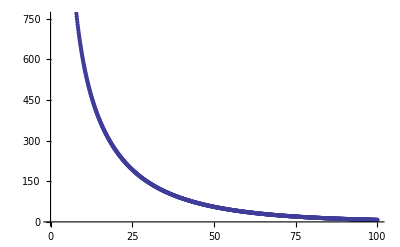

```mathematica
gp=ListPlot[fp]
```